```mathematica
currTime=0;
totalSteps=500;
tf=30;
ti=0.1;
ℏ=1;
ω=1;
m=1;

xmin=-4.5;xmax=4.5;pmin=-4.5;pmax=4.5;
nbox=40;
npoints=2;
cutoff=0.0001;
nmax=10;
L=1;
```

```mathematica
V[x_]=1/2 m ω^2 x^2;
```

```mathematica
hamonicOscEnergy[n_]:=ℏ ω(1/2+n);
infSqWellEnergy[n_]=n^2 π^2 ℏ^2/(2m L^2);
calculateTimeFactor[n_, t_]:=ⅇ^(-ⅈ hamonicOscEnergy[n] t/ℏ)
generateNthHarmonicOscillatorEigenstateWithT[n_]:=1/(√(2^n n!))((m  ω)/(π ℏ))^(1/4)ⅇ^((-(m ω x^2))/(2 ℏ))HermiteH[n, √(m ω/ℏ)x]calculateTimeFactor[n, t];
```

```mathematica
currTime=0.1;
tStep=0.1;
ℏ=1;
ω=1;
m=1;
nMin=1;
nMax=5;
num=10;

(*when := you have a different definition*)
generateNthHarmonicOscillatorEigenstate[n_]:=1/(√(2^n n!))((m  ω)/(π ℏ))^(1/4)ⅇ^((-(m ω x^2))/(2 ℏ))HermiteH[n, √(m ω/ℏ)x];



(*Function to take in wavefunction and convert into a Wigner Function

to ask: is this valid syntax*)
WignerFunction[f_, t_]:=1/(π ℏ)Integrate[Conjugate[f[(x+y), t]]f[(x-y), t] ⅇ^(2 ⅈ p y/ℏ), {y, -∞, ∞},Assumptions->{x∈Reals, p∈Reals, t∈ Reals}]

hamonicOscEnergy[n_]:=ℏ ω(1/2+n);
calculateTimeFactor[n_, t_]:=ⅇ^(-ⅈ hamonicOscEnergy[n] t/ℏ)

generateNthHarmonicOscillatorEigenstateWithT[n_]:=1/(√(2^n n!))((m  ω)/(π ℏ))^(1/4)ⅇ^((-(m ω x^2))/(2 ℏ))HermiteH[n, √(m ω/ℏ)x]calculateTimeFactor[n, t];


A=1/(√2)
B=1/(√2)
C1=1/(√3)
D1=√(2/3)
Ψ1[x_, t_]=A*generateNthHarmonicOscillatorEigenstateWithT[1]+B*generateNthHarmonicOscillatorEigenstateWithT[2];

Ψ2[x_, t_]=C1*generateNthHarmonicOscillatorEigenstateWithT[1]+D1*generateNthHarmonicOscillatorEigenstateWithT[2];
WignerFunction[f_, t_]:=1/(π ℏ)Integrate[Conjugate[f[(x+y), t]]f[(x-y), t] ⅇ^(2 ⅈ p y/ℏ), {y, -∞, ∞},Assumptions->{x∈Reals, p∈Reals, t∈ Reals}]
WignerFunctionWDomain[f_, t_]:=1/(π ℏ)Integrate[Conjugate[f[(x+y), t]]f[(x-y), t] ⅇ^(2 ⅈ p y/ℏ), {y, -∞, ∞},Assumptions->{x∈Reals, p∈Reals, t∈ Reals}]
```

1/(√2)

1/(√2)

1/(√3)

√(2/3)

```mathematica
ti=0.1
W1[x_, p_,t_]=WignerFunction[Ψ1, ti];
W2[x_, p_,t_]=WignerFunction[Ψ2, ti];
```

0.1

```mathematica
Plot3D[W1[x,p,0.1],{x,-4.5,4.5},{p,-4.5,4.5},PlotRange->All]
```

-Graphics3D-

```mathematica
Clear[p,x,W]
timeEvolve[f_,V_, ti_,tf_, nmax_]:=NDSolve[{D[W[x, p, t],t]==-p/m D[W[x, p, t],x]+Sum[(1/2)^(2n)1/((2n+1)!)(D[V[x],{x,2n+1} ])(D[W[x,p,t],{p,2n+1}]),{n,0,nmax}], W[xmin,p,t]==0,W[xmax,p,t]==0, W[x,pmin,t]==0,W[x,pmax,t]==0,W[x,p,0]==f[x,p, 0]},W[x,p,t],{x,xmin,xmax},{p,pmin,pmax},{t,ti, tf}];
```

```mathematica
snap=timeEvolve[W1, V, ti, tf, nmax];
snap1=timeEvolve[W2, V,ti,  tf, nmax];
```

Power::infy: Infinite expression 1/0.^3 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

Power::infy: Infinite expression 1/0.^3 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"]
coords=First[InterpolatingFunctionCoordinates[First[snap]]];
vals=InterpolatingFunctionValuesOnGrid[First[snap]];
```

InterpolatingFunctionValuesOnGrid[{W[x,p,t]→InterpolatingFunction[{{-4.5, 4.5}, {-4.5, 4.5}, {0.5, 30.}}, <>][x,p,t]}]

```mathematica
grid=Transpose[{coords,vals}];
partGrid=Partition[grid,4,1];
pw=Piecewise@Join[{{InterpolatingPolynomial[#,x],#[[1,1]]<=x<#[[-2,1]]}}&@partGrid[[1]],Table[{InterpolatingPolynomial[i,x],i[[2,1]]<=x<i[[-2,1]]},{i,partGrid[[2;;-2]]}],{{InterpolatingPolynomial[#,x],#[[2,1]]<=x<=#[[-1,1]]}}&@partGrid[[-1]]]
```

Transpose::nmtx: The first two levels of {{W[x, p, t] -> InterpolatingFunction[<<2>>][x, p, t]}, <<32>>d[<<1>>]} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Part::partw: Part 1 of Transpose[] does not exist.

InterpolatingPolynomial::list: List expected at position 1 in InterpolatingPolynomial[Transpose[]⟦1⟧,x].

Part::partw: Part 1 of Transpose[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through -2 in Transpose[].

Table::iterb: Iterator {i,Transpose[]⟦2;;-2⟧} does not have appropriate bounds.

InterpolatingPolynomial::list: List expected at position 1 in InterpolatingPolynomial[Transpose[]⟦-1⟧,x].

Part::partd: Part specification Transpose[]⟦-1⟧⟦2,1⟧ is longer than depth of object.

Part::partd: Part specification Transpose[]⟦-1⟧⟦-1,1⟧ is longer than depth of object.

Join::heads: Heads List and Table at positions 1 and 2 are expected to be the same.

Piecewise::pairs: The first argument Join[{{InterpolatingPolynomial[Transpose[]⟦1⟧,x],Transpose[]⟦1⟧⟦1,1⟧≤x<Transpose[]⟦1⟧⟦-2,1⟧}},Table[{InterpolatingPolynomial[i,x],i⟦2,1⟧≤x<i⟦-2,1⟧},{i,Transpose[]⟦2;;-2⟧}],{{InterpolatingPolynomial[Transpose[]⟦-1⟧,x],Transpose[]⟦-1⟧⟦2,1⟧≤x≤Transpose[]⟦-1⟧⟦-1,1⟧}}] of Piecewise is not a list of pairs.

Piecewise[Join[({{InterpolatingPolynomial[#1,x],#1⟦1,1⟧≤x<#1⟦-2,1⟧}}&)[partGrid⟦1⟧],Table[{InterpolatingPolynomial[i,x],i⟦2,1⟧≤x<i⟦-2,1⟧},{i,partGrid⟦2;;-2⟧}],({{InterpolatingPolynomial[#1,x],#1⟦2,1⟧≤x≤#1⟦-1,1⟧}}&)[partGrid⟦-1⟧]]]

```mathematica
f[x_,p_,t_]=W[x,p,t]/.snap[[1]];
g[x_,p_,t_]=W[x,p,t]/.snap1[[1]];
```

```mathematica
Plot3D[f[x,p,0.1],{x,-5,5},{p,-5,5}]
```

InterpolatingFunction::dmval: Input value {-4.99929,-4.99929,0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

```mathematica
calculateEMD[finitnorm_, ffinalnorm_, t_, xmin_, xmax_,ymin_, ymax_, nbox_, gridboxcutoff_,flag_]:=Module[{dx, dy, diffarray, outboxes, inboxes, nout, nin, nvars, mat0, supplyamount, demandamount, mat, distance, k, l, m, n, i, j},dx=(xmax-xmin)/nbox;dy=(ymax-ymin)/nbox;
diffarray=Table[Re[finitnorm[xmin+(i-1)*dx+dx/2,pmin+(j-1)*dy+dy/2,t]-ffinalnorm[xmin+(i-1)*dx+dx/2,pmin+(j-1)*dy+dy/2,t]]*dx*dy,{i,1,nbox},{j,1,nbox}];
(*Monitor[
diffarray=Table[NIntegrate[Re[f[x,p,0.1]-g[x,p,0.1]],{x,xmin+(i-1)*dx,xmin+i*dx},{p,pmin+(j-1)*dy,pmin+j*dy},Method->{"AdaptiveMonteCarlo",MaxPoints->10^7}],{i,1,nbox},{j,1,nbox}],i];*)

outboxes={};inboxes={}; 
For[i=1,i≤nbox,i++,
For[j=1,j≤nbox,j++,
If[diffarray[[i,j]]>gridboxcutoff,AppendTo[outboxes,{xmin+(i-.5)*dx,ymin+(j-.5)*dy}]];
If[diffarray[[i,j]]<-gridboxcutoff,AppendTo[inboxes,{xmin+(i-.5)*dx,ymin+(j-.5)*dy}]]]];
nout=Length[outboxes];nin=Length[inboxes];
nvars=nout*nin;
supplyamount ={}; demandamount = {};
For[i=1,i≤nbox,i++,
For[j=1,j≤nbox,j++,
If[diffarray[[i,j]]>gridboxcutoff,AppendTo[supplyamount,diffarray[[i,j]]]];
If[diffarray[[i,j]]<-gridboxcutoff,AppendTo[demandamount,diffarray[[i,j]]]];
]];
mat = Table[
EuclideanDistance[outboxes[[o]], inboxes[[q]]],{o,Length@outboxes},{q, Length@inboxes}];
mat0 = Table[0,{Length@outboxes+Length@inboxes},{Length@outboxes+Length@inboxes}];
For[i=1,i<=Length@outboxes,i++,
For[j=Length@outboxes+1,j≤(Length@inboxes+Length@outboxes),j++,
mat0[[i,j]]=mat[[i,j-Length@outboxes]]
]];

mat0//MatrixForm;

(*Then put in the numbers for the upper left section*)
For[k=1,k<=Length@outboxes,k++,
For[l=k+1,l≤Length@outboxes,l++,
mat0[[k,l]]=EuclideanDistance[outboxes[[k]], outboxes[[l]]]
]];

mat0//MatrixForm;
(*For the lower right..*)
For[m=Length@outboxes+1,m≤(Length@inboxes+Length@outboxes-1),m++,
For[n=m+1,n≤(Length@inboxes+Length@outboxes),n++,
mat0[[m,n]]=EuclideanDistance[inboxes[[m-Length@outboxes]], inboxes[[n-Length@outboxes]]]
]];

mat0//MatrixForm;
Print["done non EMD stuff"];
(*If[flag==8,Print[supplyamount];
Print[demandamount];Print[mat0];];*)
distance=FindMinimumCostFlow[ mat0, Join[supplyamount,demandamount]];
Print["done one"];
Return[distance];
]
```

done non EMD stuff

done one

done non EMD stuff

done one

done non EMD stuff

done one

done non EMD stuff

done one

done non EMD stuff

done one

done non EMD stuff

done one

done non EMD stuff

done one

done non EMD stuff

done one

done non EMD stuff

done one

done non EMD stuff

done one

done non EMD stuff

done one

done non EMD stuff

done one

done non EMD stuff

done one

done non EMD stuff

done one

done non EMD stuff

done one

done non EMD stuff

done one

done non EMD stuff

done one

done non EMD stuff

done one

done non EMD stuff

done one

done non EMD stuff

done one

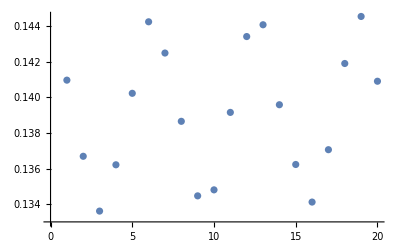

6.91148

```mathematica
(*ti=0.1;*)
tf=20;
Tn=10;
deltaT=(tf-ti)/Tn;
nbox=30;
gridboxcutoff=.0001;
thelist=
Timing[Table[calculateEMD[f, g,t1, xmin, xmax,pmin, pmax, nbox, gridboxcutoff, 8],{t1,ti, tf}]];
ListPlot[thelist[[2]]]
thelist[[1]]
```

```mathematica
ListPlot[thelist[[2]]]
```

-Graphics-

Im[(ⅇ^(-2000 ⅈ p+p x ⅈ2) (-ⅈ+2000 p+2000000 ⅈ p^2+ⅇ^(4000 ⅈ p) (ⅈ+2000 p-2000000 ⅈ p^2)))/p^3]/(4 π)

```mathematica
timeEvolve2[f_,V_, ti_,tf_, nmax_,K_]:=DSolve[{D[W[x, p, t],t]==-p/m D[W[x, p, t],x]+Integrate[K[x,j]*W[x,p-j,t],{j,pmin,pmax}], W[xmin,p,t]==0,W[xmax,p,t]==0, W[x,pmin,t]==0,W[x,pmax,t]==0,W[x,p,ti]==f[x,p, ti]},W[x,p,t],{x,xmin,xmax},{p,pmin,pmax},{t,ti, tf}];
```

```mathematica
Vt[p_]=Integrate[V[x] ⅇ^(-ⅈ p x/ℏ),{x,xmin,xmax}];
K[x_,p_]=2/(π ℏ^2)Im[Vt[2p]*ⅇ^(ⅈ2*p x/ℏ)]
```

Im[(ⅇ^((0.-9. ⅈ) p+p x ⅈ2) ((0.-2. ⅈ)+9. (2.+(0.+9. ⅈ) p) p-1. 2.71828^(18 ⅈ p) ((0.-2. ⅈ)-18. p+(0.+81. ⅈ) p^2)))/p^3]/(8 π)

```mathematica
snap=timeEvolve2[W1, V, ti, tf, nmax];
snap1=timeEvolve2[W2, V,ti,  tf, nmax];
```

```mathematica
timeEvolve2[W1, V, ti, tf, nmax,K]
```

$Aborted